```mathematica
w1[θ_,r_]:=Sin[θ-ArcTan[((√3)/2-Sin[θ])/(r-1-Cos[θ])]]
```

```mathematica
w2[θ_,r_]:=Sin[θ+ArcTan[Sin[θ]/(r-1-Cos[θ])]]
```

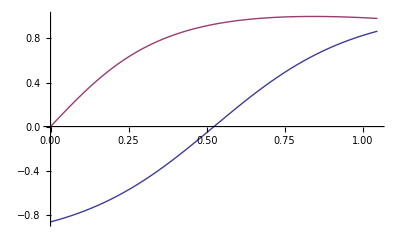

```mathematica
Plot[{w1[θ,2.5],w2[θ,2.5]},{θ,0,π/3}]
```

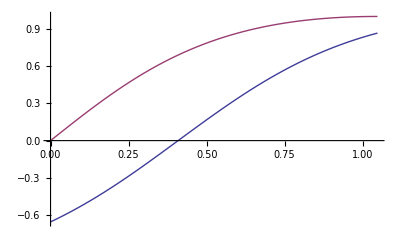

```mathematica
Plot[{w1[θ,3],w2[θ,3]},{θ,0,π/3}]
```

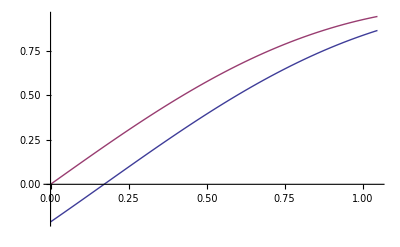

```mathematica
Plot[{w1[θ,6],w2[θ,6]},{θ,0,π/3}]
```

```mathematica
FullSimplify[D[w2[θ,r],θ]]
```

```mathematica
w2prime[θ_,r_]:=((-1+r) (-1+r-Cos[θ]) Cos[θ+ArcCot[(-1+r-Cos[θ]) Csc[θ]]])/(2+(-2+r) r-2 (-1+r) Cos[θ])
```

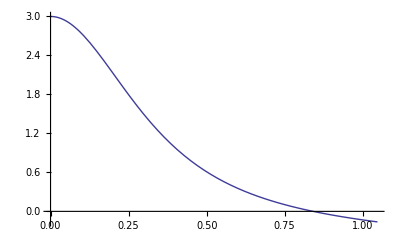

```mathematica
Plot[w2prime[θ,2.5],{θ,0,π/3}]
```

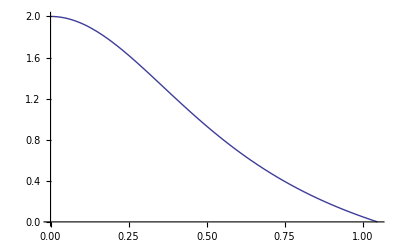

```mathematica
Plot[w2prime[θ,3],{θ,0,π/3}]
```

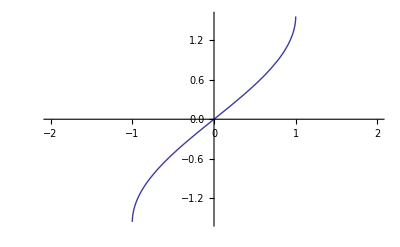

```mathematica
Plot[ArcSin[x],{x,-2,2}]
```

```mathematica
(***************)
```

```mathematica
α[n_,m_]:=Which[n==1&&m==2,0,n==2&&m==3,(2π)/3,n==3&&m==1,(4π)/3,n==2&&m==1,π,n==3&&m==2,(5π)/3,n==1&&m==3,π/3]
```

```mathematica
α[3,2]
```

(5 π)/3

```mathematica
wnext[w_,θ_,n_,m_,r_]:=w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]])
```

```mathematica
T[w_,θ_,n_,m_,r_]:={w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]]),Mod[θ+π+ArcSin[w] +ArcSin[wnext[w,θ,n,m,r]] ,2π]}
```

```mathematica
T[0.45,0.45,1,2,2.1]
```

{-1.21664,2.48756+0.6469 ⅈ}

```mathematica
T2[w_,θ_,n_,m_,r_]:=Composition[T,T][w,θ,n,m,r]
```

```mathematica
T2[0.1, 0.2, ]
```

```mathematica
T[0.1,0.2,1,2,3]
```

-0.78704

```mathematica
T[-0.7870404381907682,2.5357633313989965,2,3,3]
```

{0.557232,5.36241}

```mathematica
T[0.5572317476793701,5.362407488061782,3,1,3]
```

{-2.38657,1.24107+1.5159 ⅈ}

```mathematica
f[w_,θ_]:=T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[2]],3,1,3]-{w,θ}
```

```mathematica
f[0.1,0.2]
```

{-2.48657,1.04107+1.5159 ⅈ}

```mathematica
π/6//N
```

0.523599

```mathematica
f[-0.5,π/6]
```

{-2.33147×10^-15,-2.33147×10^-15}

```mathematica
FindRoot[{f[w,θ][[1]]==0,f[w,θ][[2]]==0},{{w,-0.4},{θ,0.5}}]
```

{w→-0.5-3.5756×10^-16 ⅈ,θ→0.523599+2.81703×10^-16 ⅈ}

```mathematica
FindRoot[{f[w,θ][[1]]==0,f[w,θ][[2]]==0},{{w,-0.9},{θ,0.9}}]
```

{w→-0.5-2.93284×10^-16 ⅈ,θ→0.523599+2.45544×10^-16 ⅈ}

```mathematica
FindRoot[f[w,θ],{{w,-0.4},{θ,0.4}}]
```

{w→-0.5-6.16283×10^-17 ⅈ,θ→0.523599+5.31379×10^-17 ⅈ}

```mathematica
(** abac = 1213 **)
```

```mathematica
f4[w_,θ_]:=T[T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],1,2,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],1,2,3][[2]],1,3,3][[1]],T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],1,2,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],1,2,3][[2]],1,3,3][[2]],3,1,3]-{w,θ}
```

```mathematica
FindRoot[{f4[w,θ][[1]]==0,f4[w,θ][[2]]==0},{{w,0.2},{θ,1.2}},Assuming->{Element[w,Reals],Element[θ,Reals]}]
```

FindRoot::optx: Unknown option Assuming in FindRoot[{f4[w, θ] ⟦ 1 ⟧ == 0, f4[w, θ] ⟦ 2 ⟧ == 0}, {{w, 0.2`}, {θ, 1.2`}}, Assuming → {w ∈ Reals, θ ∈ Reals}].

FindRoot[{f4[w,θ]⟦1⟧==0,f4[w,θ]⟦2⟧==0},{{w,0.2},{θ,1.2}},Assuming→{w∈Reals,θ∈Reals}]

```mathematica
NSolve[{f4[w,θ][[1]]==0,f4[w,θ][[2]]==0},{w,θ}]
```

$Aborted

```mathematica
NSolve[{f[w,θ][[1]]==0,f[w,θ][[2]]==0},{w,θ}]
```

$Aborted

```mathematica
f4[0.2, 1.2]
```

{-35.1287-15.6444 ⅈ,2.87743+6.00703 ⅈ}

```mathematica
Plot3D[T[w,θ,1,2,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[2]],3,1,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[f[w,θ]==0,{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
f[-0.5,π/6]
```

{-2.33147×10^-15,-2.33147×10^-15}

```mathematica
FullSimplify[T[Sin[ϕ],θ,n,m,r],ϕ>-π/2&&ϕ<π/2]
```

{Sin[ϕ]-r Sin[θ+ϕ-Which[n==1&&m==2,0,n==2&&m==3,(2 π)/3,n==3&&m==1,(4 π)/3,n==2&&m==1,π,n==3&&m==2,(5 π)/3,n==1&&m==3,π/3]],Mod[π+θ+ϕ+ArcSin[Sin[ϕ]-r Sin[θ+ϕ-Which[n==1&&m==2,0,n==2&&m==3,(2 π)/3,n==3&&m==1,(4 π)/3,n==2&&m==1,π,n==3&&m==2,(5 π)/3,n==1&&m==3,π/3]]],2 π]}

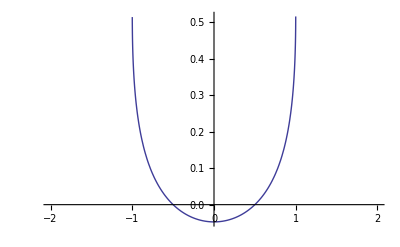

```mathematica
Plot[ArcSin[x]/x-π/3,{x,-2,2}]
```

```mathematica
T[-0.5,π/6,1,3,1]
```

{0.366025,3.51633}

```mathematica
T[0.3660254037844386,3.516327086298533,3,1,1]
```

{0.659375,1.46946}

```mathematica
f1[w_,θ_]:=T[T[w,θ,1,3,1][[1]],T[w,θ,1,3,1][[2]],3,1,1]-{w,θ}
```

```mathematica
f1[-0.5,π/6]
```

{1.15937,0.945857}

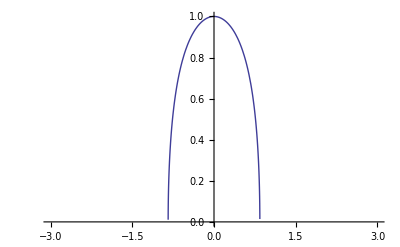

```mathematica
Plot[√(1-ArcSin[x]^2),{x,-3,3}]
```

```mathematica
Sin[1]//N
```

0.841471

```mathematica
Plot3D[√(1-x^2)ArcSin[y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[√(1-(x y)^2)ArcSin[y-x],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
f4[x_,y_]:=√(1-(x y)^2)ArcSin[y-x]
```

```mathematica
f4[Interval[{0,1}],Interval[{-0.4,0.3}]]
```

ArcSin[Interval[{-1.4,0.3}]] Interval[{0.916515,1}]

```mathematica
Interval[{0,1}]-Interval[{-0.4,0.3}]
```

Interval[{-0.3,1.4}]

```mathematica
ArcSin[Interval[{-1.4000000000000004,0.3000000000000001}]] //N
```

ArcSin[Interval[{-1.4,0.3}]]

```mathematica
w1:=Interval[{-5.04187500000000000033*10^-01,-5.02249999999999999993*10^-01}]
```

```mathematica
θ1:=Interval[{5.19411275598298799959*10^-01,5.21348775598298800054*10^-01}]
```

```mathematica
T[w1,θ1,1,2,3]
```

{Interval[{-0.4896374651543408949,-0.4751615811322693207}],Mod[Interval[{2.6208891397604132938,2.6415949642549472745}],2 π]}

```mathematica
Plot3D[ArcSin[x-y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[√(x+y),{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Interval[{-2,0},{1,4}]-Interval[{1,2}]
```

Interval[{-4,3}]

```mathematica
Interval[{-2,0},{1,4}]+Interval[{1,2}]
```

Interval[{-1,6}]

```mathematica
Interval[{-2,0}] - Interval[{1,2}]
```

Interval[{-4,-1}]

```mathematica
Interval[{1,4}] - Interval[{1,2}]
```

Interval[{-1,3}]

```mathematica
Interval[{-2,0},{1,4}]+Interval[{1,2},{5,7}]
```

Interval[{-1,11}]

```mathematica
Interval[{-2,0}]+Interval[{1,2}]
```

Interval[{-1,2}]

```mathematica
Interval[{-2,0}]+Interval[{5,7}]
```

Interval[{3,7}]

```mathematica
Interval[{1,4}]+Interval[{1,2}]
```

Interval[{2,6}]

```mathematica
Interval[{1,4}]+Interval[{5,7}]
```

Interval[{6,11}]

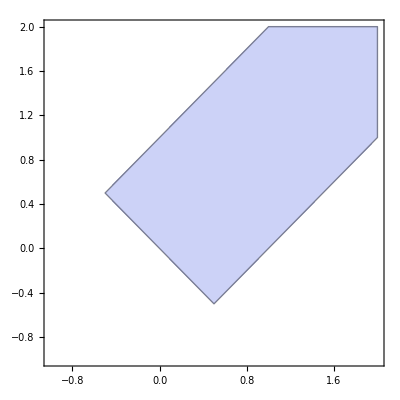

```mathematica
RegionPlot[Abs[x-y]≤1&&x+y>0,{x,-1,2},{y,-1,2}]
```

```mathematica
rect[x1_,x2_,y1_,y2_]:=RegionPlot[x>x1&&x<x2&&y>y1&&y<y2,{x,-2,8},{y,-2,8},PlotStyle->Red]
```

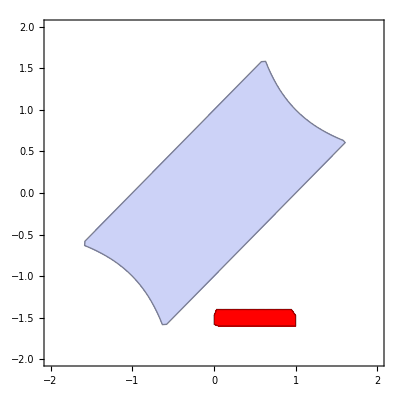

```mathematica
Show[RegionPlot[Abs[x-y]≤1&&Abs[x y]<1,{x,-2,2},{y,-2,2}],rect[0,1,-1.6,-1.4]]
```

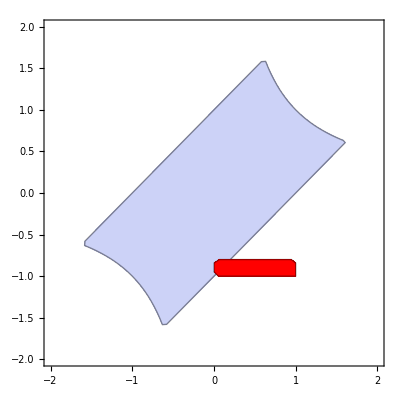

```mathematica
Show[RegionPlot[Abs[x-y]≤1&&Abs[x y]<1,{x,-2,2},{y,-2,2}],rect[0,1,-1,-0.8]]
```

```mathematica
Plot3D[√(ArcSin[y-x](1-(x y)^2)),{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

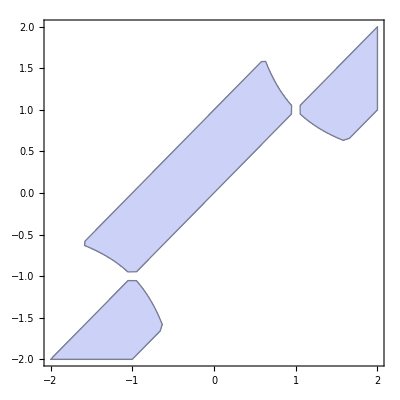

```mathematica
RegionPlot[ArcSin[y-x](1-(x y)^2)>0,{x,-2,2},{y,-2,2}]
```

```mathematica
(* Domain of [arcsin(Subscript[x, 1]-Subscript[x, 2])-π/2, √(Subscript[x, 1]+Subscript[x, 2])-3] *)
```

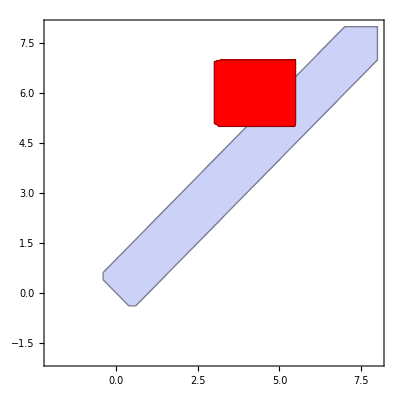

```mathematica
Show[RegionPlot[Abs[x-y]<1&&x+y≥0,{x,-2,8},{y,-2,8}],rect[3,5.5,5,7]]
```

```mathematica
ftest1[x_]:={ArcSin[x[[1]]-x[[2]]]-π/2,√(x[[1]]+x[[2]])-3}
```

```mathematica
ftest1[{2,3}]
```

{-π,-3+√5}

```mathematica
ftest1[{5,4}]
```

{0,0}

```mathematica
FindRoot[ftest1[x]==0,{x,{4.2,3.4}}]
```

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→{4.99213+0. ⅈ,3.99213+0. ⅈ}}

```mathematica
ftest1[{4.992131233907286,3.9921318761660394}]
```

{-0.00113337,-0.00262396}

```mathematica
FindRoot[ftest1[{x,y}]=={0,0},{{x,4.2},{y,3.4}}]
```

{x→5.+0. ⅈ,y→4.+0. ⅈ}

```mathematica
points:={{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082}}
```

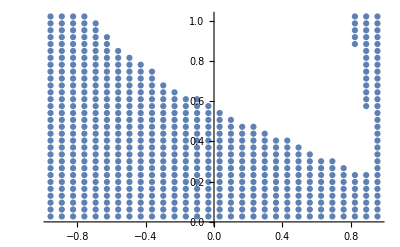

```mathematica
ListPlot[points]
```

```mathematica
points2:={{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082}}
```

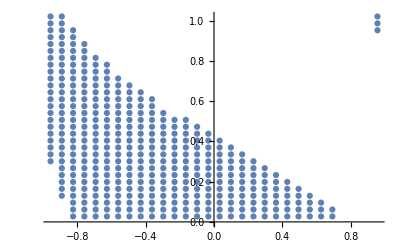

```mathematica
ListPlot[points2]
```

```mathematica
points3:={{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-9.569999999999999999999999999999999999999999999999999999999999999999999999999849*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-8.909999999999999999999999999999999999999999999999999999999999999999999999999916*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-8.249999999999999999999999999999999999999999999999999999999999999999999999999983*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-7.589999999999999999999999999999999999999999999999999999999999999999999999999877*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{-6.929999999999999999999999999999999999999999999999999999999999999999999999999858*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{-6.269999999999999999999999999999999999999999999999999999999999999999999999999925*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-5.609999999999999999999999999999999999999999999999999999999999999999999999999819*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-4.949999999999999999999999999999999999999999999999999999999999999999999999999886*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-4.289999999999999999999999999999999999999999999999999999999999999999999999999694*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{-3.629999999999999999999999999999999999999999999999999999999999999999999999999718*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-2.969999999999999999999999999999999999999999999999999999999999999999999999999698*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-2.309999999999999999999999999999999999999999999999999999999999999999999999999657*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-1.649999999999999999999999999999999999999999999999999999999999999999999999999638*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{-9.899999999999999999999999999999999999999999999999999999999999999999999999995972*10^-02,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{-3.299999999999999999999999999999999999999999999999999999999999999999999999995779*10^-02,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{3.300000000000000000000000000000000000000000000000000000000000000000000000004415*10^-02,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{9.900000000000000000000000000000000000000000000000000000000000000000000000006228*10^-02,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{1.650000000000000000000000000000000000000000000000000000000000000000000000000653*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{2.310000000000000000000000000000000000000000000000000000000000000000000000000694*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{2.970000000000000000000000000000000000000000000000000000000000000000000000000648*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{3.630000000000000000000000000000000000000000000000000000000000000000000000000711*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{4.29000000000000000000000000000000000000000000000000000000000000000000000000073*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{4.950000000000000000000000000000000000000000000000000000000000000000000000000663*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{5.610000000000000000000000000000000000000000000000000000000000000000000000000855*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{6.270000000000000000000000000000000000000000000000000000000000000000000000000788*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{6.930000000000000000000000000000000000000000000000000000000000000000000000000721*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{7.590000000000000000000000000000000000000000000000000000000000000000000000000827*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{8.25000000000000000000000000000000000000000000000000000000000000000000000000076*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{8.910000000000000000000000000000000000000000000000000000000000000000000000000779*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.711995918660996000000000000000000000000000000000000000000000000000000000000139*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.135987755982988000000000000000000000000000000000000000000000000000000000000418*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.559979593304980000000000000000000000000000000000000000000000000000000000000562*10^-02},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.298397143062697200000000000000000000000000000000000000000000000000000000000065*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.640796326794896400000000000000000000000000000000000000000000000000000000000117*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.983195510527095600000000000000000000000000000000000000000000000000000000000126*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.325594694259294800000000000000000000000000000000000000000000000000000000000135*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,2.667993877991494000000000000000000000000000000000000000000000000000000000000144*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.01039306172369320000000000000000000000000000000000000000000000000000000000024*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.352792245455892400000000000000000000000000000000000000000000000000000000000249*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,3.695191429188091600000000000000000000000000000000000000000000000000000000000258*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.037590612920290800000000000000000000000000000000000000000000000000000000000267*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.379989796652490000000000000000000000000000000000000000000000000000000000000319*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,4.722388980384689200000000000000000000000000000000000000000000000000000000000328*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.06478816411688840000000000000000000000000000000000000000000000000000000000038*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.40718734784908760000000000000000000000000000000000000000000000000000000000026*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,5.749586531581286800000000000000000000000000000000000000000000000000000000000398*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.09198571531348600000000000000000000000000000000000000000000000000000000000045*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.434384899045685200000000000000000000000000000000000000000000000000000000000416*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,6.776784082777884400000000000000000000000000000000000000000000000000000000000468*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.119183266510083600000000000000000000000000000000000000000000000000000000000607*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.461582450242282800000000000000000000000000000000000000000000000000000000000486*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,7.803981633974482000000000000000000000000000000000000000000000000000000000000625*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.146380817706681200000000000000000000000000000000000000000000000000000000000504*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.488780001438880400000000000000000000000000000000000000000000000000000000000643*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,8.831179185171079600000000000000000000000000000000000000000000000000000000000695*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.173578368903278800000000000000000000000000000000000000000000000000000000000661*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.515977552635478000000000000000000000000000000000000000000000000000000000000713*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,9.858376736367677200000000000000000000000000000000000000000000000000000000000592*10^-01},{9.570000000000000000000000000000000000000000000000000000000000000000000000000885*10^-01,1.020077592009987640000000000000000000000000000000000000000000000000000000000082}}
```

```mathematica
ListPlot[points3]
```

-Graphics-